# The Volterra Function

## whose derivative is Riemann Non-integrable

```mathematica
ClearAll["Global`*"];
```

## The Smith-Volterra-Cantor Set

In this section, we construct several iterations of Smith-Volterra-Cantor set by marking its pair of points  indicating the interval being removed.

```mathematica
ClearAll[SVC,SVCG];
SVC[0] = {0,1};
SVC[n_]:=If[n>0,Sort@Flatten[ Join[Table[If[OddQ[k] && k<Length[SVC[n-1]],{(SVC[n-1][[k]]+SVC[n-1][[k+1]])/2-1/(2 4^n),(SVC[n-1][[k]]+SVC[n-1][[k+1]])/2+1/(2 4^n)},Nothing],{k,1,Length[SVC[n-1]]}],SVC[n-1]]],
SVC[0]];
```

```mathematica
SVC[4]
```

{0,9/128,11/128,5/32,7/32,37/128,39/128,3/8,5/8,89/128,91/128,25/32,27/32,117/128,119/128,1}

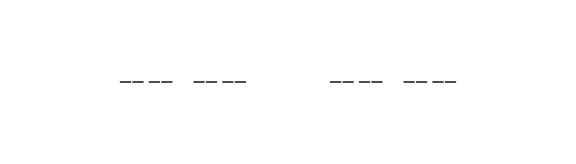

```mathematica
SVCG = SVC[4];

Graphics[Table[If[OddQ[k],Line[{{SVCG[[k]],0},{SVCG[[k+1]],0}}]],{k,1,Length[SVCG]}],ImageSize->Large,PlotRange->{{-0.2,1.2},{-0.2,0.2}}]
```

## The Volterra Function

The Volterra function is constructed recursively, by using .

Consider subinterval , find the maximum zero  for the derivative of  in this interval, and make a piecewise defined function  such that  on  but  on . Define the function  symmetrically on , set  elsewhere, and shift the graph of  to the right by the amount , such that the  .

Consider subinterval , find the maximum zero  for the derivative of  inside of this interval, and make a piecewise defined function  such that  on  but  on . Define the function  symmetrically on , set  elsewhere, and shift the graph of  to the right by the amount  and  respectively.

Do the same thing again and again.

The Volterra function is defined by adding altogether all such functions.

```mathematica
Chi[a_,b_,x_]:=Piecewise[{{1,a< x < b}},0];
V[a_,b_,x_]:=Module[{z},z = Max[u/.NSolve[2u Sin[1/u]-Cos[1/u]==0 && u>(b-a)/100&& u < (b-a)/2,u]]; (x-a)^2 Sin[1/(x-a)]  Chi[a,a+z,x] +(b-x)^2 Sin[1/(b-x)] Chi[b-z,b,x]+z^2 Sin[1/z] Chi[a+z,b-z,x]];
Vd[a_,b_,x_]:=Module[{z},z = Max[u/.NSolve[2u Sin[1/u]-Cos[1/u]==0 && u>(b-a)/100&& u < (b-a)/2,u]]; (2(x-a)Sin[1/(x-a)]-Cos[1/(x-a)])  Chi[a,a+z,x] +(2(b-x)Sin[1/(b-x)]-Cos[1/(b-x)]) Chi[b-z,b,x]];
```

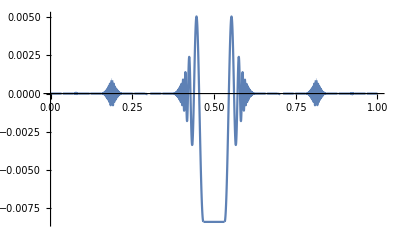
{45.7245,-Graphics-}

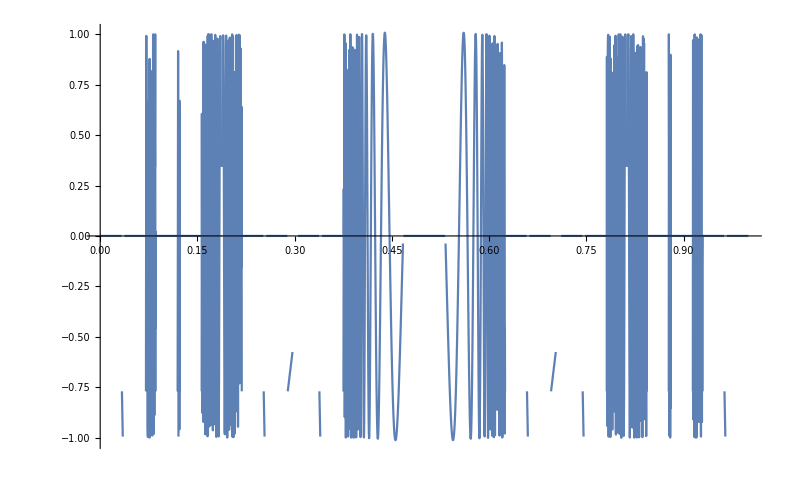
{46.0275,-Graphics-}

```mathematica
Volterra[x_]:= Sum[If[OddQ[k],0,V[SVCG[[k]],SVCG[[k+1]],x]],{k,1,Length[SVCG]-1}];
DVolterra[x_]:= Sum[If[OddQ[k],0,Vd[SVCG[[k]],SVCG[[k+1]],x]],{k,1,Length[SVCG]-1}];

Plot[Evaluate[Volterra[x]],{x,0,1},PlotRange-> All]//AbsoluteTiming
Plot[Evaluate[DVolterra[x]],{x,0,1},PlotRange-> All]//AbsoluteTiming
```